# Complex Analysis

## De Moivre’s Theorem

#### [r( cos θ + ⅈ (sin θ )])^n = r^n(cos nθ + ⅈ sin nθ) Let r = 1 and n = 2

```mathematica
Grid[#,Frame-> All]&@Table[{Cos[n θ],ComplexExpand@Re@((Cos[θ]+ ⅈ Sin[θ])^n),Sin[n θ],ComplexExpand@Im@((Cos[θ]+ ⅈ Sin[θ])^n)},{n,7}]
```

Cos[θ] | Cos[θ] | Sin[θ] | Sin[θ]
Cos[2 θ] | Cos[θ]^2-Sin[θ]^2 | Sin[2 θ] | 2 Cos[θ] Sin[θ]
Cos[3 θ] | Cos[θ]^3-3 Cos[θ] Sin[θ]^2 | Sin[3 θ] | 3 Cos[θ]^2 Sin[θ]-Sin[θ]^3
Cos[4 θ] | Cos[θ]^4-6 Cos[θ]^2 Sin[θ]^2+Sin[θ]^4 | Sin[4 θ] | 4 Cos[θ]^3 Sin[θ]-4 Cos[θ] Sin[θ]^3
Cos[5 θ] | Cos[θ]^5-10 Cos[θ]^3 Sin[θ]^2+5 Cos[θ] Sin[θ]^4 | Sin[5 θ] | 5 Cos[θ]^4 Sin[θ]-10 Cos[θ]^2 Sin[θ]^3+Sin[θ]^5
Cos[6 θ] | Cos[θ]^6-15 Cos[θ]^4 Sin[θ]^2+15 Cos[θ]^2 Sin[θ]^4-Sin[θ]^6 | Sin[6 θ] | 6 Cos[θ]^5 Sin[θ]-20 Cos[θ]^3 Sin[θ]^3+6 Cos[θ] Sin[θ]^5
Cos[7 θ] | Cos[θ]^7-21 Cos[θ]^5 Sin[θ]^2+35 Cos[θ]^3 Sin[θ]^4-7 Cos[θ] Sin[θ]^6 | Sin[7 θ] | 7 Cos[θ]^6 Sin[θ]-35 Cos[θ]^4 Sin[θ]^3+21 Cos[θ]^2 Sin[θ]^5-Sin[θ]^7

## Complex Mappings

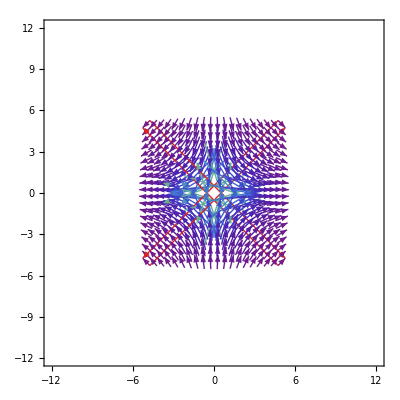
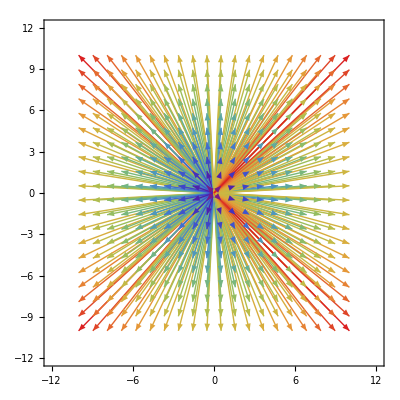
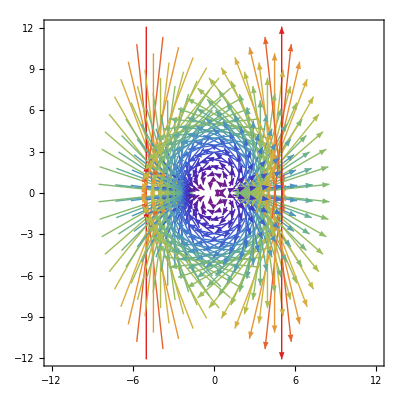
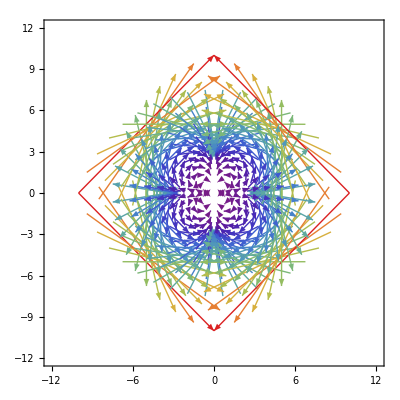
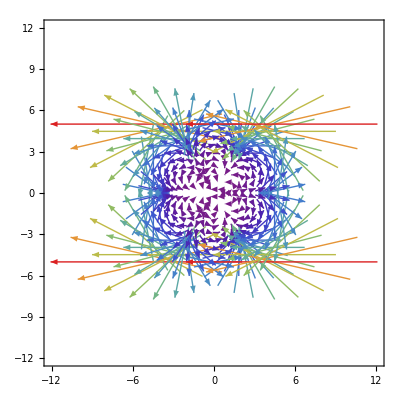
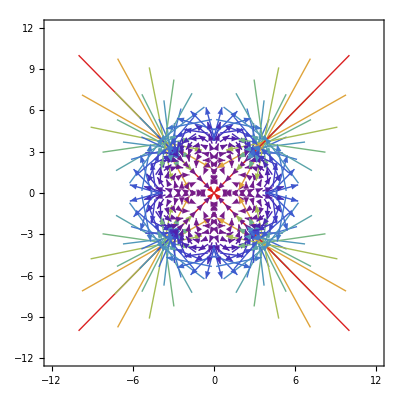
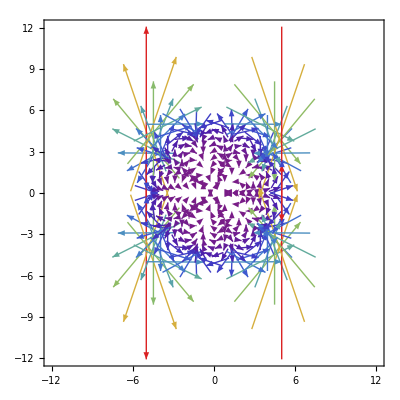
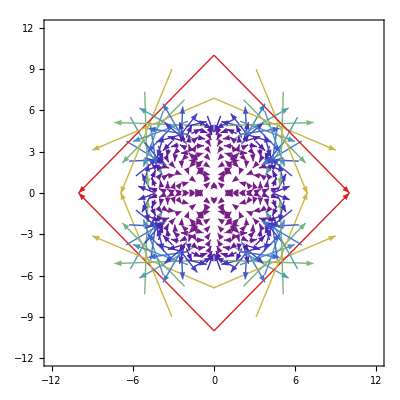
-1
-Graphics-1
-Graphics-2
-Graphics-3
-Graphics-4
-Graphics-5
-Graphics-6
-Graphics-7
-Graphics-8
-Graphics-9
-Graphics-

```mathematica
Row@Table[Column[#,Center]&@{Style[n,25],VectorPlot[{ComplexExpand@Re@#,ComplexExpand@Im@#},{x,-5,5},{y,-5,5},VectorScale->{1,Scaled[.2]},VectorPoints->20,VectorColorFunction->"Rainbow",ImageSize->{225}]&@((x + ⅈ y)^n)},{n,{-1,1,2,3,4,5,6,7,8,9}}]
```

## Complex Derivatives (Cauchy-Riemann Equations)

#### Let w = f(z) = u(x,y) + ⅈ v(x,y), then f.b4(z_0) = ⅆw/ⅆz= lim__(Δz→0)Δw/Δz = lim__(Δz→0)(f(z_0+Δz)-f(z_0))/Δz, and therefore if f(z) is differentiable in z_0, then the limit exists and is the same in any direction. Since f(z) = u(x,y) + ⅈ v(x,y), we check ∂_x f and ∂_y f for conditions of differentiability. We know: f.b4(z_0) = lim__(Δz→0)[ (Δu + ⅈ Δv)/(Δx + ⅈ Δy)], then: For Δy = 0: f.b4(z_0) = lim__(Δz→0)[ Δu/Δx+ⅈ Δv/Δx] = (∂u)/(∂x)+ⅈ(∂v)/(∂x), For Δx = 0: f.b4(z_0) = lim__(Δz→0)[ Δu/(ⅈ Δy)+Δv/Δy]= (∂v)/(∂y)-ⅈ(∂u)/(∂y), and therefore, since the limit must be the same in any direction, the following system must hold for a differentiable/analytic function: (∂u)/(∂x) = (∂v)/(∂y) & (∂v)/(∂x)= -(∂u)/(∂y)

## Laplace’s Equation ((∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)=0)

#### If u + ⅈ v is analytic then, u_x = v_y & v_x = -u_y, Differentiating by x and y respectively: u_xx = v_yx & v_xy = -u_yy, therefore for a complex analytic function, both u and v satisfy Laplace’s equation separately.

## Invertibility

#### Let f(z) = u + ⅈ v be analytic, then the Jacobian: |J| =|(∂(u,v))/(∂(x,y))|= |u_x | u_y v_x | v_y|= u_x v_y-u_y v_x ↔ u_x^2+v_x^2=|f'(z)|^2 therefore, f is invertible as long as its magnitude is non-zero.

## Conformal Mappings

#### An invertible mapping is conformal if it preserves angles. The angle θ between two vectors of equal length, Δz_1 and Δz_2, in the Argand diagram is given by θ=Δz_2/Δz_1 Let f(z) = u + ⅈ v be analytic and non-zero, then lim _(Δz_1→ 0) Δw_1/Δz_1=lim _(Δz_2→ 0) Δw_2/Δz_2 ⇒lim _(Δz_1, Δz_2→ 0) Δz_2/Δz_1=lim _(Δw_1, Δw_2→ 0) Δw_2/Δw_1 therefore, analytic mappings are conformal. Let T = T(u(x,y),v(x,y)), then through the chain rule, the Laplacian of T: T_xx+T_yy = T_u(u_xx+u_yy)+T_v(v_xx+v_yy) + T_uu(u_x^2+u_y^2)+T_vv(v_x^2+v_y^2)+2T_uv(u_x v_x+u_y v_y) If T is analytic, then: u_xx+u_yy = v_xx+v_yy = 0, u_x v_x+u_y v_y → u_x(-u_y) + u_y(v_x) = 0, u_x^2+u_y^2 = v_x^2+v_y^2 = |f'(z)|^2, Therefore, we have: T_xx+T_yy = (T_uu+T_vv)|f'(z)|^2

## Sequences and Series

#### e^z= e^(x + ⅈ y)= e^x ∑_(n=0)^∞ (ⅈy)^n/(n!)= e^x[cos(y) + ⅈ sin(y)] Then, u = e^x cos(y) & v = e^x sin(y) ⇒ u^2+ v^2=e^(2x) & v = u tan(y)

## Finding the Image of a Set Under a Mapping

#### Given: set A as an equation/inequality in x and y, mapping f(z) = w = u + ⅈ v Goal: Using inverse functions, represent the image set B in terms of u and v Example: f(z) = ⅈ z=w A = {(x,y) :y = x+1} · f(z)∈B ⇔ f^-1(w)=z∈A · Let w = u+ⅈ v · f^-1(w) = -ⅈ w=v-ⅈ u · f(z)∈B ⇔ f^-1(w)=v-ⅈ u∈A ·f(z)∈B ⇔ (v,-u)∈A ·f(z)∈B ⇔ (v,-u)∈A ·x→ v ·y→-u ·y=x+1→-u=v+1 B = {(u,v):v = -u-1} Example: D_1(-1,-1) ={z:|z+1+ⅈ|<1} f(z) = w=(3-4ⅈ)z+6+2ⅈ f^-1(w) = z=(w-6-2ⅈ)/(3-4ⅈ) z=(w-6-2ⅈ)/(3-4ⅈ)∈D_1(-1,-1)iff |(w-6-2ⅈ)/(3-4ⅈ)+1+ⅈ|<1 z∈D_1(-1,-1)iff |(w+1-3ⅈ)/(3-4ⅈ)|<5

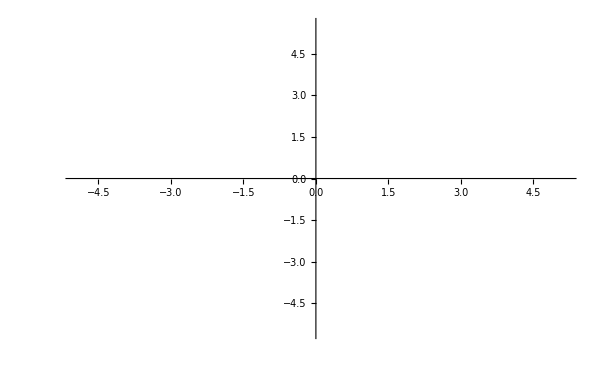

```mathematica
k = 1/2+  0ⅈ;
Show[{
ListLinePlot[Table[ReIm[Exp[(nx+ⅈ ny)]],{nx,-3,3,.1},{ny,-3,3,.1}],ImageSize->600,PlotStyle->White],
ListLinePlot[Transpose[Table[ReIm[Exp[(nx+ⅈ ny)]],{nx,-3,3,.1},{ny,-3,3,.1}]],ImageSize->600,PlotStyle->White]
}]
```

```mathematica
Off[Power::infy]
Manipulate[{
k = a + b ⅈ;
Show[{
ListLinePlot[Table[ReIm[Exp[(nx+ⅈ ny)]],{nx,-π,π,.1},{ny,-π,π,.1}],ImageSize->600,PlotStyle->White],
ListLinePlot[Transpose[Table[ReIm[Exp[(nx+ⅈ ny)]],{nx,-π,π,.1},{ny,-π,π,.1}]],ImageSize->600,PlotStyle->White]
}]},{{a,1},-2,2},{{b,0},-π,π}]
```

```mathematica
b= 0;
complexstuff = Table[ Show[{
ListLinePlot[Table[ReIm[(nx+ⅈ ny)^(a+ ⅈ b)],{nx,-5,5,.1},{ny,-5,5,.1}],ImageSize->600,PlotStyle->Black,PlotRange->{{-10,10},{-10,10}}],
ListLinePlot[Transpose[Table[ReIm[(nx+ⅈ ny)^(a+ ⅈ b)],{nx,-5,5,.1},{ny,-5,5,.1}]],ImageSize->600,PlotStyle->Black,PlotRange->{{-10,10},{-10,10}}]
}],{a,0,3, .05}];
Export["complexstuff.gif", complexstuff]
```

Power::indet: Indeterminate expression (0.+0. ⅈ)^0. encountered.

$Aborted

complexstuff.gif

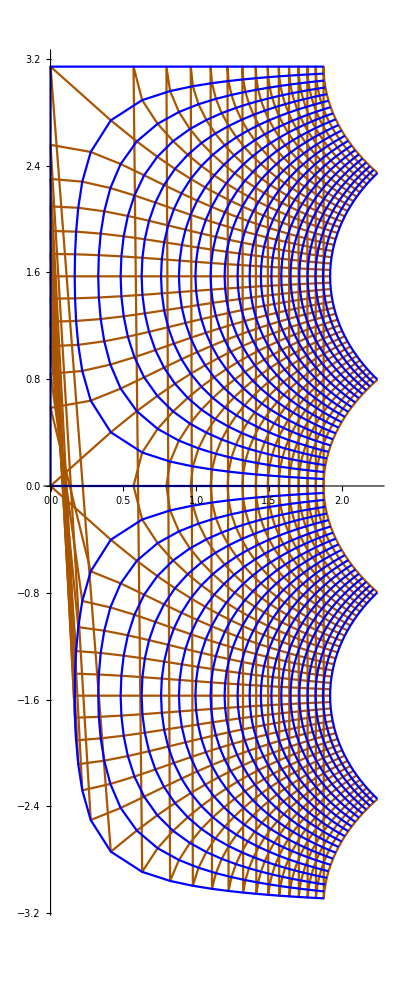

```mathematica
L = 2;
dL = .1;
f[nx_,ny_]:=(z = nx + ⅈ ny;
ArcCosh[z/(.6)])
Quiet@Show[{
ListLinePlot[Table[ReIm[f[nx,ny]],{nx,-L,L,dL},{ny,-L,L,dL}],ImageSize->400,PlotStyle->Darker@Orange,AspectRatio->{1,1},PlotRange->Full],
ListLinePlot[Transpose[Table[ReIm[f[nx,ny]],{nx,-L,L,dL},{ny,-L,L,dL}]],ImageSize->400,PlotStyle->Blue,AspectRatio->{1,1}]
}]
```